```mathematica
(*Final*)
```

```mathematica
(* -------------- Math functions ---------------*)
CompareEachElements[vec1_,vec2_]:=Table[vec1[[i]]==vec2[[i]],{i,1,Length[vec1]}];
Rotz4[θ_]:=({{Cos[θ], -Sin[θ], 0, 0}, {Sin[θ], Cos[θ], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})
Rotz[θ_]:=({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}})
Vec3[v1_,v2_,v3_]:={{v1},{v2},{v3}}
Trans4[x_,y_]:=({{1, 0, 0, x}, {0, 1, 0, y}, {0, 0, 1, 0}, {0, 0, 0, 1}})
NewT4[x_,y_,θ_]:=Trans4[x,y].Rotz4[θ]
Zeros[dim1_,dim2_]:=Table[0,{i,1,dim1},{j,1,dim2}]
MF[T_]:=MatrixForm[T]

(* Skew funcs *)
Hat[ω_]:=({{0, -ω[[3,1]], ω[[2,1]]}, {ω[[3,1]], 0, -ω[[1,1]]}, {-ω[[2,1]], ω[[1,1]], 0}})
Unhat[ω_]:={{ω[[3,2]]},{ω[[1,3]]},{ω[[2,1]]}}

(* generalized hat: g -> twist *)
Genhat2[ω_,v_]:=ArrayFlatten[({{Hat[ω], v}, {Zeros[1,3], 0}})]
Genhat[S_]:=Module[{ω,v},
ω=S[[1;;3,1;;1]];
v=S[[4;;6,1;;1]];
Genhat2[ω,v]
]
GenUnhat[T_]:=Join[Unhat[T[[1;;3,1;;3]]],T[[1;;3,4;;4]]]
AdT[T_]:=Module[{R,p},
R=T[[1;;3,1;;3]];
p=T[[1;;3,4;;4]];
ArrayFlatten[({{R, Zeros[3,3]}, {Hat[p].R, R}})]
]
InvT[T_]:=Module[{R,p},
R=T[[1;;3,1;;3]];
p=T[[1;;3,4;;4]];
ArrayFlatten[({{Transpose[R], -Transpose[R].p}, {Zeros[1,3], 1}})]
]
(* ----------- Math funcs ends here. ---------------;-------------- Below are the main program. --------------*)
```

```mathematica
(* Properties *)
nObjects=3;
l=l1=l2=l3=1;
w=w1=w2=w3=0.25;
masses=ConstantArray[1,nObjects];
inertias=ConstantArray[1,nObjects];
lens={l1,l2,l3};
widths={w1,w2,w3};
g=9.8;
```

```mathematica
(* Vars *)
qs={x[t],y[t],θ1[t],θ2[t],θ3[t]};
qsvars={x,y,θ1,θ2,θ3};
nVars=Length[qs];
(* Simulation's init condition *)
qsInit={0,l/2+l*Cos[Pi/20],0,Pi/20,-Pi/20};
dqsInit=ConstantArray[0,nVars];
dqs=D[qs,t];
ddqs=D[dqs,t];
```

```mathematica
(* ----------------------------- *)
(* Transformation matrices *)
Ts={T1,T2,T3};

 (* Geometry *)
Tw=Trans4[0,0];
T0End=Tw.Trans4[x[t],y[t]];

T1=T0End.Rotz4[θ1[t]]//Simplify;
T1End=T1.Trans4[0,-l1/2];
p1End=T1.Transpose[{{0,l2/2,0,1}}]//Simplify;

T2=T1End.Rotz4[Pi+θ2[t]].Trans4[0,l2/2]//Simplify;
p2End=T2.Transpose[{{0,l2/2,0,1}}]//Simplify;

T3=T1End.Rotz4[Pi+θ3[t]].Trans4[0,l3/2]//Simplify;
p3End=T3.Transpose[{{0,l3/2,0,1}}]//Simplify;
```

```mathematica
(* --------------- Left side of EL eqs -------------- *)
(* Body generalized mass, composed of Inertia Tensor and Mass Matrix *)
getGb[j_,m_]:=ArrayFlatten[({{DiagonalMatrix[{j,j,j}], Zeros[3,3]}, {Zeros[3,3], DiagonalMatrix[{m,m,m}]}})]
Gbs=Table[getGb[inertias[[i]],masses[[i]]],{i,1,nObjects}]//Simplify;
(* Body screw axis *)
Vbs=Table[GenUnhat[InvT[Ts[[i]]].D[Ts[[i]],t]],{i,1,nObjects}]//Simplify;
(* Lagrange Equations: Kinetic and Potential Energy *)
GetKE[Gb_,Vb_]:=(1/2*Transpose[Vb].Gb.Vb)[[1,1]];
GetPE[m_,T_]:=m*g*T[[2,4]];
KEs=Table[GetKE[Gbs[[i]],Vbs[[i]]],{i,1,nObjects}]//Simplify;
PEs=Table[GetPE[masses[[i]],Ts[[i]]],{i,1,nObjects}]//Simplify;
Lag=Total[Join[KEs,-PEs]]//Simplify;
(* Left side of Euler-Lagrange Equations*)
ELeqsLeft=D[D[Lag,{dqs}],t]-D[Lag,{qs}]//Simplify;
```

```mathematica
(* --------------- Right side of EL eqs -------------- *)
(* Constraints *)
(*conslink1x=p1End[[1,1]]+l/2*Cos[Pi/20]; (* x=0 *)
conslink2x=p2End[[1,1]]-l*Sin[Pi/20]; (* x=0 *)
conslink3x=p3End[[1,1]]+l*Sin[Pi/20]; (* x=0 *)
conslink1y=p1End[[2,1]];(* y=0 *)*)
conslink2y=p2End[[2,1]];(* y=0 *)
conslink3y=p3End[[2,1]];(* y=0 *)
cons={conslink2y,conslink3y}//Simplify;
nCons=Length[cons];
If[nCons>0,
(λs=Transpose[{Table[Symbol["$λ"<>ToString@i],{i,nCons}]}];
consgrad=Transpose[Grad[cons,qs]]; (* Grad[2,5]->Mat(2,5),Transpose->(5,2)*)
consddt=D[D[cons,t],t]//Simplify)];
```

```mathematica
(* External forces *)
externalForces=ConstantArray[0,nVars];
Clear[Fθ2,Fθ3,θ2d,θ3d]
k1=10;
k2=20;
xd=0;yd=0;
θ1d=0;
θ2d=Pi/20+Pi/3*Sin[t/2]^2;
θ3d=-Pi/20-Pi/3*Sin[t/2]^2;
Fθ2=-k1(θ1[t]-θ1d)-k2(θ2[t]-θ2d);
Fθ3=-k1(θ1[t]-θ1d)-k2(θ3[t]-θ3d);
externalForces={0,0,0,Fθ2,Fθ3};
(*externalForces={0,0,0,0,0};*)
```

```mathematica
(* ----------------------------- *)
(* Solve *)
If[nCons>0,(* with constraints *)
(EulerLagEqs=Thread[ELeqsLeft==Flatten[consgrad.λs]+externalForces]//Simplify;
consddtEqs=Thread[consddt==ConstantArray[0,nCons]];
EQ=Solve[Join[EulerLagEqs,consddtEqs],Join[ddqs,Flatten[λs]]]),
(* No constraint *)
EulerLagEqs=Thread[ELeqsLeft==externalForces]//Simplify;
EQ=Solve[EulerLagEqs,ddqs]];
```

```mathematica
(* NDsolve *)
timeend=10;
ddqSolve=CompareEachElements[ddqs,EQ[[1,;;,2]]];
q0Solve=CompareEachElements[qs/.t->0,qsInit];
dq0Solve=CompareEachElements[dqs/.t->0,dqsInit];
sim=NDSolve[{ddqSolve,q0Solve,dq0Solve},qsvars,{t,0,timeend},Method->{"EquationSimplification"->"Residual"}];
```

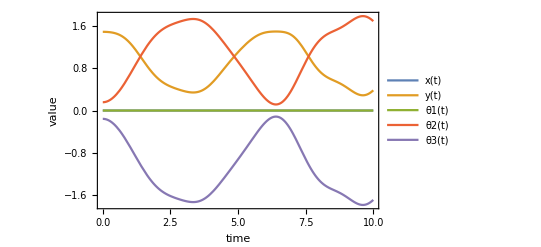

```mathematica
(* ----------------------------- *)
(* Plot curve *)
curves={qs/.sim[[1]]}//Flatten;
Plot[curves,{t,0,timeend},PlotStyle->{Thick},PlotLegends->qs,PlotRange->Automatic,Frame->True,FrameLabel->{"time","value"}]
```

```mathematica
plotLink[T_,k_]:=Module[{p0,p1,p2,p3,p4,p,pw,l,w},
l=lens[[k]];
w=widths[[k]];
p0={-w/2,l/2,0,1};
p1={w/2,l/2,0,1};
p2={w/2,-l/2,0,1};
p3={-w/2,-l/2,0,1};
p4={-w/2,l/2,0,1};
p={p0,p1,p2,p3,p4};
pw=(T.Transpose[p])[[1;;2,;;]];
Table[Line[{pw[[1;;2,i]],pw[[1;;2,i+1]]}],{i,1,4}](* {Line1,Line2,...]}*)
]
links=FullSimplify[Table[plotLink[Ts[[i]],i],{i,1,nObjects}]];
Clear[linkssim];
linkssim[tt_]:=(Table[(links[[i]]/.sim)[[1]],{i,1,Length[links]}])/.t->tt;
Animate[Show[
{Graphics[linkssim[t]]
},PlotRange-> {{-3,3},{-3,3}},Frame-> True],{t,0,timeend}]
```